```mathematica
(* export function for plot figures *)
<<peeters`

(*relative to ~/physicsplay*)
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

peeters`

/Users/pjoot/project/figures/GAelectrodynamics

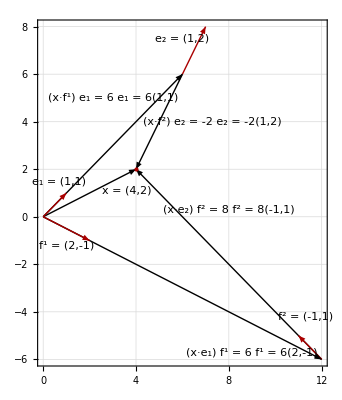

```mathematica
ClearAll["Global`*"]
Block[{x, e1, e2, f1, f2, xe, xf, o},
o = {0, 0} ;
x = {4, 2} ;
e1 = {1, 1} ;
e2 = {1, 2} ;
f1 = {2, -1};
f2 = {-1, 1} ;
xf = {x . f1, x . f2 } ;
xe = {x . e1, x . e2 } ;

(* check dot products *)
(*{{e1. f1, e2 . f2, e1 . f2, e2 . f1} ,*)

Graphics[ 
{
Arrow[{o, x}]

, Arrow[{o, xe[[1]] f1}]
, Arrow[{xe[[1]] f1, xe[[1]] f1 + xe[[2]] f2}]
, Arrow[{o, xf[[1]] e1}]
, Arrow[{xf[[1]] e1, xf[[1]] e1 + xf[[2]] e2}]

, Darker[Red]
, Arrow[{o,  f1}]
, Arrow[{xe[[1]] f1, xe[[1]] f1 +  f2}]
, Arrow[{o,  e1}]
, Arrow[{xf[[1]] e1, xf[[1]] e1 + e2}]


,PointSize[Large]
, Point[x]

, Black
, Text["x = (4,2)",{3.6,1.1}]
, Text[ "(x·e_1) f^1 = 6 f^1 = 6(2,-1)", 6 f1 + {-3, 0.3} ]
, Text[ "(x·e_2) f^2 = 8 f^2 = 8(-1,1)", 6 f1 + 4 f2  + {0, 2.3}]
, Text[ "(x·f^1) e_1 = 6 e_1 = 6(1,1)", 6  e1 + {-3, -1}]
, Text[ "(x·f^2) e_2 = -2 e_2 = -2(1,2)", 6 e1 -e2 + {2.3, 0}]

, Text[ "f^1 = (2,-1)",  f1  + {-1, -0.2}]
, Text[ "f^2 = (-1,1)", 6 f1 +  f2 +{0.3, 0.8} ]
, Text[ "e_1 = (1,1)",   e1  + {-0.3, 0.5}]
, Text[ "e_2 = (1,2)", 6 e1 +e2 + {-1, -0.5}]

}
, Frame->True
, GridLines->Automatic
, GridLinesStyle->Directive[Orange,Dashed]
]
(*}*)
]
```

```mathematica
ClearAll["Global`*"]
beta := 1/3
gamma := 1/Sqrt[1 - beta^2]
f0 := gamma {1, beta} 
f1 := gamma{beta, 1}
xt := 2 beta
xx := 3 beta /2
xP := {xt, xx}
xX := gamma ( xx - xt beta)
xT := gamma ( xt - xx beta )
xProj := f1 xX
tProj := f0 xT
Graphics[ 
{Arrow[{{0,0}, f0}]
, Arrow[{{0, 0}, f1} ]
,Arrow[{ tProj, xP}]
, Arrow[{xProj, xP}]
, Text[ Subscript[f,0], {beta+0.1, 1}]
,Text[ Subscript[f,1], {1, beta+0.1}]
, Point[xP]
, Text["x", xP+{0.02,0.02}]
, Text[Times[CenterDot[x,Subscript[f,0]],Superscript[f,0]], xP+{0.09,-0.05}]
, Text[Times[CenterDot[x,Subscript[f,1]],Superscript[f,1]], xP+{-0.2,0.0}]
}
, Frame->True
,  GridLines->Automatic
, GridLinesStyle->Directive[Orange,Dashed]
]
```

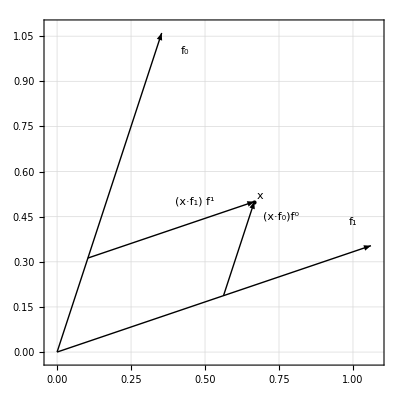

Set::setraw: Cannot assign to raw object "e_0".

### Dynamic oblique.

```mathematica
Manipulate[
DynamicModule[{(*x, e1, e2,*) f1, f2, xe, xf, o, r, s, ao, to, esub, esuper, bold, proj, rproj},
o = {0, 0} ;
ao = {0,.15} ;
to[x_] = Offset[{20,0},x] ;
(*s = {0.3, 0.3} ;*)
s = o ;
bold = Style[ #, Bold] &;
esub = Subscript[bold["e"], #] &;
esuper = Superscript[bold["e"], #] &;
proj = Row[{"(", bold["x"], "·", esuper[#], ")", esub[#]}] &;
rproj = Row[{"(", bold["x"], "·", esub[#], ")", esuper[#]}] &;

r= Inverse[{ e1, e2} ];
f1 = Part[r, All, 1] ;
f2 = Part[r, All, 2] ;

xf = {x . f1, x . f2 } ;
xe = {x . e1, x . e2 } ;

Graphics[{
Arrow[{o, x}, ao]

, Arrow[{o, xe[[1]] f1}, ao]
, Arrow[{xe[[1]] f1, xe[[1]] f1 + xe[[2]] f2}, ao]
, Arrow[{o, xf[[1]] e1}, ao]
, Arrow[{xf[[1]] e1, xf[[1]] e1 + xf[[2]] e2}, ao]

, Darker[Red]
, Arrow[{o,  f1}, ao]
, Arrow[{xe[[1]] f1, xe[[1]] f1 +  f2}, ao]
, Arrow[{o,  e1}, ao]
, Arrow[{o,  e2}, ao]
, Arrow[{xf[[1]] e1, xf[[1]] e1 + e2}, ao]

, Black

, Text[bold["x"],to[x (*+ {0.5, 0.3}*)],Background->White]

, Text[ esub[1], to[e1  + s],Background->White]
, Text[ esub[2], to[e2 + s ],Background->White]
, Text[ esub[2], to[xf[[1]] e1 +e2 + s],Background->White]

, Text[ esuper[1],  to[f1  + s],Background->White]
, Text[ esuper[2],  to[xe[[1]] f1+  f2 + s] ,Background->White]

, Text[ rproj[1], to[xe[[1]]  f1/2 + s] ,Background->White]
, Text[ rproj[2], to[xe[[1]]  f1 +  xe[[2]] f2 /2 + s],Background->White]
, Text[ proj[1], to[xf[[1]]  e1 /2+ s],Background->White]
, Text[ proj[2], to[xf[[1]] e1 +xf[[2]]e2 /2+ s],Background->White]

}
, Frame->True
, GridLines->Automatic
, GridLinesStyle->Directive[Orange,Dashed]
,BaseStyle->16 (* this changes the font, making it bigger *)
]

] 
, {{x,{4,2}},Locator}
, {{e1,{1,1}},Locator}
, {{e2,{1, 2}},Locator}
, {{o2, {4,8}}, Locator}
]
```

```mathematica
sn2 = DynamicModule[{e1={1.41,1.1199999999999992},e2={0.8699999999999999,2.0199999999999996},x={4,2}},DynamicModule[{f1,f2,xe,xf,o,r,s,ao,to},o={0,0};ao={0,0.15};to[x_]=Offset[{20,0},x];s=o;r=Inverse[{e1,e2}];f1=r⟦All,1⟧;f2=r⟦All,2⟧;xf={x.f1,x.f2};xe={x.e1,x.e2};Graphics[{Arrow[{o,x},ao],Arrow[{o,xe⟦1⟧ f1},ao],Arrow[{xe⟦1⟧ f1,xe⟦1⟧ f1+xe⟦2⟧ f2},ao],Arrow[{o,xf⟦1⟧ e1},ao],Arrow[{xf⟦1⟧ e1,xf⟦1⟧ e1+xf⟦2⟧ e2},ao],Darker[Red],Arrow[{o,f1},ao],Arrow[{xe⟦1⟧ f1,xe⟦1⟧ f1+f2},ao],Arrow[{o,e1},ao],Arrow[{o,e2},ao],Arrow[{xf⟦1⟧ e1,xf⟦1⟧ e1+e2},ao],Black,Text["x",to[x],Background->White],Text["\!\(\*SubscriptBox[\(e\), \(1\)]\)",to[e1+s],Background->White],Text["\!\(\*SubscriptBox[\(e\), \(2\)]\)",to[e2+s],Background->White],Text["\!\(\*SubscriptBox[\(e\), \(2\)]\)",to[xf⟦1⟧ e1+e2+s],Background->White],Text["\!\(\*TemplateBox[{\"e\",\"1\"},\n\"Superscript\"]\)",to[f1+s],Background->White],Text["\!\(\*TemplateBox[{\"e\",\"2\"},\n\"Superscript\"]\)",to[xe⟦1⟧ f1+f2+s],Background->White],Text["(x·\!\(\*SubscriptBox[\(e\), \(1\)]\)) \!\(\*TemplateBox[{\"e\",\"1\"},\n\"Superscript\"]\)",to[1/2 xe⟦1⟧ f1+s],Background->White],Text["(x·\!\(\*SubscriptBox[\(e\), \(2\)]\)) \!\(\*TemplateBox[{\"e\",\"2\"},\n\"Superscript\"]\)",to[xe⟦1⟧ f1+1/2 xe⟦2⟧ f2+s],Background->White],Text["(x·\!\(\*TemplateBox[{\"e\",\"1\"},\n\"Superscript\"]\)) \!\(\*SubscriptBox[\(e\), \(1\)]\)",to[1/2 xf⟦1⟧ e1+s],Background->White],Text["(x·\!\(\*TemplateBox[{\"e\",\"2\"},\n\"Superscript\"]\)) \!\(\*SubscriptBox[\(e\), \(2\)]\)",to[xf⟦1⟧ e1+1/2 xf⟦2⟧ e2+s],Background->White]},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],BaseStyle->16]]]
```

```mathematica
sn = DynamicModule[{e1={1.41,1.1199999999999992},e2={0.665,1.3200000000000003},x={4,2}},DynamicModule[{f1,f2,xe,xf,o,r,s,ao,to},o={0,0};ao={0,0.15};to[x_]=Offset[{20,0},x];s=o;r=Inverse[{e1,e2}];f1=r⟦All,1⟧;f2=r⟦All,2⟧;xf={x.f1,x.f2};xe={x.e1,x.e2};Graphics[{Arrow[{o,x},ao],Arrow[{o,xe⟦1⟧ f1},ao],Arrow[{xe⟦1⟧ f1,xe⟦1⟧ f1+xe⟦2⟧ f2},ao],Arrow[{o,xf⟦1⟧ e1},ao],Arrow[{xf⟦1⟧ e1,xf⟦1⟧ e1+xf⟦2⟧ e2},ao],Darker[Red],Arrow[{o,f1},ao],Arrow[{xe⟦1⟧ f1,xe⟦1⟧ f1+f2},ao],Arrow[{o,e1},ao],Arrow[{o,e2},ao],Arrow[{xf⟦1⟧ e1,xf⟦1⟧ e1+e2},ao],Black,Text["x",to[x],Background->White],Text["\!\(\*SubscriptBox[\(e\), \(1\)]\)",to[e1+s],Background->White],Text["\!\(\*SubscriptBox[\(e\), \(2\)]\)",to[e2+s],Background->White],Text["\!\(\*SubscriptBox[\(e\), \(2\)]\)",to[xf⟦1⟧ e1+e2+s],Background->White],Text["\!\(\*TemplateBox[{\"e\",\"1\"},\n\"Superscript\"]\)",to[f1+s],Background->White],Text["\!\(\*TemplateBox[{\"e\",\"2\"},\n\"Superscript\"]\)",to[xe⟦1⟧ f1+f2+s],Background->White],Text["(x·\!\(\*SubscriptBox[\(e\), \(1\)]\)) \!\(\*TemplateBox[{\"e\",\"1\"},\n\"Superscript\"]\)",to[1/2 xe⟦1⟧ f1+s],Background->White],Text["(x·\!\(\*SubscriptBox[\(e\), \(2\)]\)) \!\(\*TemplateBox[{\"e\",\"2\"},\n\"Superscript\"]\)",to[xe⟦1⟧ f1+1/2 xe⟦2⟧ f2+s],Background->White],Text["(x·\!\(\*TemplateBox[{\"e\",\"1\"},\n\"Superscript\"]\)) \!\(\*SubscriptBox[\(e\), \(1\)]\)",to[1/2 xf⟦1⟧ e1+s],Background->White],Text["(x·\!\(\*TemplateBox[{\"e\",\"2\"},\n\"Superscript\"]\)) \!\(\*SubscriptBox[\(e\), \(2\)]\)",to[xf⟦1⟧ e1+1/2 xf⟦2⟧ e2+s],Background->White]},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],BaseStyle->16]]]
```

```mathematica
(* snapshot for figure *)
Block[{pp},
pp = DynamicModule[{e1={1,1},e2={1,2},x={4,2}},DynamicModule[{f1,f2,xe,xf,o,r,s,ao,to},o={0,0};ao={0,0.15};to[x_]=Offset[{20,0},x];s=o;r=Inverse[{e1,e2}];f1=r⟦All,1⟧;f2=r⟦All,2⟧;xf={x.f1,x.f2};xe={x.e1,x.e2};Graphics[{Arrow[{o,x},ao],Arrow[{o,xe⟦1⟧ f1},ao],Arrow[{xe⟦1⟧ f1,xe⟦1⟧ f1+xe⟦2⟧ f2},ao],Arrow[{o,xf⟦1⟧ e1},ao],Arrow[{xf⟦1⟧ e1,xf⟦1⟧ e1+xf⟦2⟧ e2},ao],Darker[Red],Arrow[{o,f1},ao],Arrow[{xe⟦1⟧ f1,xe⟦1⟧ f1+f2},ao],Arrow[{o,e1},ao],Arrow[{o,e2},ao],Arrow[{xf⟦1⟧ e1,xf⟦1⟧ e1+e2},ao],Black,Text["x",to[x],Background->White],Text["\!\(\*SubscriptBox[\(e\), \(1\)]\)",to[e1+s],Background->White],Text["\!\(\*SubscriptBox[\(e\), \(2\)]\)",to[e2+s],Background->White],Text["\!\(\*SubscriptBox[\(e\), \(2\)]\)",to[xf⟦1⟧ e1+e2+s],Background->White],Text["\!\(\*TemplateBox[{\"e\",\"1\"},\n\"Superscript\"]\)",to[f1+s],Background->White],Text["\!\(\*TemplateBox[{\"e\",\"2\"},\n\"Superscript\"]\)",to[xe⟦1⟧ f1+f2+s],Background->White],Text["(x·\!\(\*SubscriptBox[\(e\), \(1\)]\)) \!\(\*TemplateBox[{\"e\",\"1\"},\n\"Superscript\"]\)",to[1/2 xe⟦1⟧ f1+s],Background->White],Text["(x·\!\(\*SubscriptBox[\(e\), \(2\)]\)) \!\(\*TemplateBox[{\"e\",\"2\"},\n\"Superscript\"]\)",to[xe⟦1⟧ f1+1/2 xe⟦2⟧ f2+s],Background->White],Text["(x·\!\(\*TemplateBox[{\"e\",\"1\"},\n\"Superscript\"]\)) \!\(\*SubscriptBox[\(e\), \(1\)]\)",to[1/2 xf⟦1⟧ e1+s],Background->White],Text["(x·\!\(\*TemplateBox[{\"e\",\"2\"},\n\"Superscript\"]\)) \!\(\*SubscriptBox[\(e\), \(2\)]\)",to[xf⟦1⟧ e1+1/2 xf⟦2⟧ e2+s],Background->White]},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],BaseStyle->16]]] ;

peeters`exportForLatex["obliqueReciprocalFig1", pp]
]
```

```mathematica
Directory[]
```

C:\Users\Peeter\Documents

### Junk layout stuff.

```mathematica
Subscript[f, 0] Superscript[f, 0]
```

f_0 f^0

```mathematica
FullForm[f^0 (x·Subscript[f, 0])]
```

Times[CenterDot[x,Subscript[f,0]],Superscript[f,0]]

```mathematica
FullForm["(x·e_1) f^1 = 6 e_1 = 6(1,1)"]
"(x·e_1) f^1 = 6 e_1 = 6(1,1)"
```

"(x\[CenterDot]e_1) f^1 = 6 e_1 = 6(1,1)"

(x·e_1) f^1 = 6 e_1 = 6(1,1)

### Stackexchange MWE

```mathematica
(* how-to-position-text-labels-automatically-to-not-overlap-other-graphics-elements *)

Manipulate[DynamicModule[{f1,f2,xf,o,r,s},o={0,0};
s={0.1,0.1};
r=Inverse[{e1,e2}];f1=Part[r,All,1];f2=Part[r,All,2];
xf={x.f1,x.f2};
Graphics[{Arrow[{o,x}],Arrow[{o,xf[[1]] e1}],Arrow[{xf[[1]] e1,xf[[1]] e1+xf[[2]] e2}],Text["x",x+s],Text["e1",e1+s],Text["e2",e2+s]}]],{{x,{4,2}},Locator},{{e1,{1,1}},Locator},{{e2,{1,2}},Locator}]
```

```mathematica
(* answer by: David Carraher *)
Manipulate[DynamicModule[{f1,f2,xf,o,r,s},o={0,0};
r=Inverse[{e1,e2}];f1=Part[r,All,1];f2=Part[r,All,2];
xf={x.f1,x.f2};
Graphics[{Arrow[{o,x},{0,.15}],Arrow[{o,xf[[1]] e1},{0,.15}],Arrow[{xf[[1]] e1,xf[[1]] e1+xf[[2]] e2},{0,.15}],Text["x",Offset[{20,0},x],Background->White],Text["e1",Offset[{20,0},e1],Background->White],Text["e2",Offset[{20,0},e2],Background->White]},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],BaseStyle->16]],{{x,{4,2}},Locator},{{e1,{1,1}},Locator},{{e2,{1,2}},Locator}]
```

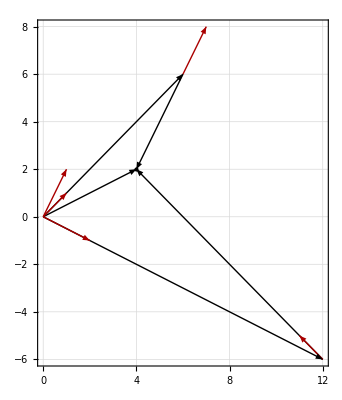

```mathematica
Clear[positionlabel, addlabels] ;

positionlabel[g_Graphics,{label_,x_}]:=Module[{p,b,bd,xi,m,ivp,sc},p=PlotRange[g];
b=ImagePad[ImagePad[Binarize@Show[g,ImagePadding->0],-1],1,Black];
bd=ImageDimensions[b];
xi=bd MapThread[Rescale,{x,p}];
m=MinFilter[b,1+Reverse[Rasterize[TraditionalForm@label,"RasterSize"]/2]];
ivp=ImageValuePositions[m,1];
sc=If[ivp=={},x,Scaled[First[Nearest[ivp,xi]]/bd]];
Graphics@Inset[label,sc,Center]]

addlabels[g_Graphics,labels_]:=Fold[Show[#1,positionlabel[##]]&,g,labels]

(*The labels must be supplied as a list like {{"label1",{x1,y1}},{"label2",{x2,y2}},...}.Here's an example:g=Plot[Sin[x],{x,0,10},Frame->True,Epilog->{PointSize[Large],Point[{#,Sin[#]}&/@Range[0,10]]}];

labels={Style[#,20],{#,Sin[#]}}&/@Range[0,10];

addlabels[g,labels]*)

Module[{x, e1, e2, f1, f2, xe, xf, o, r, s, ao, to, g, l},
o = {0, 0} ;
ao = o ;
x = {4, 2} ;
e1 = {1, 1} ;
e2 = {1, 2} ;

r= Inverse[{ e1, e2} ];
f1 = Part[r, All, 1] ;
f2 = Part[r, All, 2] ;

xf = {x . f1, x . f2 } ;
xe = {x . e1, x . e2 } ;

l = { {"x",x }
,  {"e_1", e1  }
,  {"e_2", e2  }
,  {"e_2", xf[[1]] e1 +e2 }
,  {"e^1", f1  }
,  {"e^2", xe[[1]] f1+  f2 }
,  {"(x·e_1) e^1", xe[[1]]  f1/2 }
,  {"(x·e_2) e^2", xe[[1]]  f1 +  xe[[2]] f2 /2 }
,  {"(x·e^1) e_1", xf[[1]]  e1 /2}
,  {"(x·e^2) e_2", xf[[1]] e1 +xf[[2]]e2 /2} } ;

g=Graphics[
Flatten[
{{
Arrow[{o, x}]

, Arrow[{o, xe[[1]] f1}]
, Arrow[{xe[[1]] f1, xe[[1]] f1 + xe[[2]] f2}]
, Arrow[{o, xf[[1]] e1}]
, Arrow[{xf[[1]] e1, xf[[1]] e1 + xf[[2]] e2}]

, Darker[Red]
, Arrow[{o,  f1}]
, Arrow[{xe[[1]] f1, xe[[1]] f1 +  f2}]
, Arrow[{o,  e1}]
, Arrow[{o,  e2}]
, Arrow[{xf[[1]] e1, xf[[1]] e1 + e2}]

, Black
,PointSize[ Large ]
, Point[ x ]


}, l}]
, Frame->True
, GridLines->Automatic
, GridLinesStyle->Directive[Orange,Dashed]
,BaseStyle->16 (* this changes the font, making it bigger *)
] ;

g

(*addlabels[g,l]
*)
]
```

```mathematica
peeters`exportForLatex["obliqueReciprocalFig2", sn2]
```

{obliqueReciprocalFig2.eps,obliqueReciprocalFig2pn.png}

```mathematica
Directory[]
```

C:\Users\Peeter\Documents

## Rework the manipulate for figure in reciprocal.tex

```mathematica
Manipulate[
DynamicModule[{(*x, e1, e2,*) f1, f2, xe, xf, o, r, s, ao, to, esub, esuper, bold, proj, rproj},
o = {0, 0} ;
ao = {0,.15} ;
s = 0.3 ;

to[start_, end_, ss_ :s] =  start + (end-start)(1 + ss/Norm[end-start]) ;

bold = Style[ #, Bold] &;
esub = Subscript[bold["x"], #] &;
esuper = Superscript[bold["x"], #] &;
proj = Row[{"(", bold["a"], "·", esuper[#], ")", esub[#]}] &;
rproj = Row[{"(", bold["a"], "·", esub[#], ")", esuper[#]}] &;

r= Inverse[{ e1, e2} ];
f1 = Part[r, All, 1] ;
f2 = Part[r, All, 2] ;

xf = {x . f1, x . f2 } ;
xe = {x . e1, x . e2 } ;

Graphics[{
Thick
, Arrow[{o, x}, ao]

(*Path along x_a coordinates to x*)
,Darker[Blue]
, Arrow[{o, xe[[1]] f1}, ao]
, Arrow[{xe[[1]] f1, xe[[1]] f1 + xe[[2]] f2}, ao]
, Text[ rproj[1], to[o,xe[[1]]  f1/2 ]  ,Background->White]
, Text[ rproj[2], to[o, xe[[1]]  f1 +  xe[[2]] f2 /2 ],Background->White]

(*Path along x^a coordinates to x*)
,Darker[Purple]
, Arrow[{o, xf[[1]] e1}, ao]
, Arrow[{xf[[1]] e1, xf[[1]] e1 + xf[[2]] e2}, ao]
, Text[ proj[1], to[o,xf[[1]]  e1 /2],Background->White]
, Text[ proj[2], to[o,xf[[1]] e1 +xf[[2]]e2 /2] +{0.5,0},Background->White]


(*e^1, e^2*)
, Darker[Red]
, Arrow[{o,  f1}, ao]
, Arrow[{xe[[1]] f1, xe[[1]] f1 +  f2}, ao]
, Text[ esuper[1],  to[o, f1 ],Background->White]
, Text[ esuper[2],  to[xe[[1]] f1,xe[[1]] f1+  f2 ] ,Background->White]
, Arrow[{o2,  o2+f1}, ao]
, Arrow[{o2,o2 +  f2}, ao]
, Text[ esuper[1],  to[o2,o2+f1 ],Background->White]
, Text[ esuper[2],  to[o2,o2+ f2 ] ,Background->White]


(*e_1, e_2*)
,Darker[Green]
, Arrow[{o,  e1}, ao]
, Arrow[{xf[[1]] e1, xf[[1]] e1 + e2}, ao]
, Text[ esub[1], to[o,e1 ],Background->White]
, Text[ esub[2], to[xf[[1]] e1, xf[[1]] e1 +e2],Background->White]
, Arrow[{o2,  o2+e1}, ao]
, Arrow[{o2, o2 + e2}, ao]
, Text[ esub[1], to[o2,o2+e1 ],Background->White]
, Text[ esub[2], to[o2, o2+e2],Background->White]


, Black
,PointSize[Large]
, Point[x]
, Text[bold["a"],to[o,x, 2s ],Background->White]

, Opacity[0.1]
, Brown // Lighter
, Parallelogram[ o2,{e1,f2}]
,Brown // Darker
, Parallelogram[ o2,{e2,f1}]

}
, Frame->True
, GridLines->Automatic
, GridLinesStyle->Directive[Orange,Dashed]
,BaseStyle->14 (* this changes the font, making it bigger *)
]

] 
, {{x,{4,2}},Locator}
, {{e1,{1,1}},Locator}
, {{e2,{1, 2}},Locator}
, {{o2,{8,2}},Locator}
]
```

```mathematica
sn3 = DynamicModule[{e1={1,1},e2={1,2},o2={8,2},x={4,2}},DynamicModule[{f1,f2,xe,xf,o,r,s,ao,to,esub,esuper,bold,proj,rproj},o={0,0};ao={0,0.15};s=0.3;to[start_,end_,ss_:s]=start+(end-start) (1+ss/Norm[end-start]);bold=Style[#1,Bold]&;esub=Subscript[bold["x"], #1]&;esuper=bold["x"]^#1&;proj=Row[{"(",bold["a"],"·",esuper[#1],")",esub[#1]}]&;rproj=Row[{"(",bold["a"],"·",esub[#1],")",esuper[#1]}]&;r=Inverse[{e1,e2}];f1=r⟦All,1⟧;f2=r⟦All,2⟧;xf={x.f1,x.f2};xe={x.e1,x.e2};Graphics[{Thick,Arrow[{o,x},ao],Darker[Blue],Arrow[{o,xe⟦1⟧ f1},ao],Arrow[{xe⟦1⟧ f1,xe⟦1⟧ f1+xe⟦2⟧ f2},ao],Text[rproj[1],to[o,1/2 xe⟦1⟧ f1],Background->White],Text[rproj[2],to[o,xe⟦1⟧ f1+1/2 xe⟦2⟧ f2],Background->White],Darker[Purple],Arrow[{o,xf⟦1⟧ e1},ao],Arrow[{xf⟦1⟧ e1,xf⟦1⟧ e1+xf⟦2⟧ e2},ao],Text[proj[1],to[o,1/2 xf⟦1⟧ e1],Background->White],Text[proj[2],to[o,xf⟦1⟧ e1+1/2 xf⟦2⟧ e2]+{0.5,0},Background->White],Darker[Red],Arrow[{o,f1},ao],Arrow[{xe⟦1⟧ f1,xe⟦1⟧ f1+f2},ao],Text[esuper[1],to[o,f1],Background->White],Text[esuper[2],to[xe⟦1⟧ f1,xe⟦1⟧ f1+f2],Background->White],Arrow[{o2,o2+f1},ao],Arrow[{o2,o2+f2},ao],Text[esuper[1],to[o2,o2+f1],Background->White],Text[esuper[2],to[o2,o2+f2],Background->White],Darker[Green],Arrow[{o,e1},ao],Arrow[{xf⟦1⟧ e1,xf⟦1⟧ e1+e2},ao],Text[esub[1],to[o,e1],Background->White],Text[esub[2],to[xf⟦1⟧ e1,xf⟦1⟧ e1+e2],Background->White],Arrow[{o2,o2+e1},ao],Arrow[{o2,o2+e2},ao],Text[esub[1],to[o2,o2+e1],Background->White],Text[esub[2],to[o2,o2+e2],Background->White],Black,PointSize[Large],Point[x],Text[bold["a"],to[o,x,2 s],Background->White],Opacity[0.1],Lighter[Brown],Parallelogram[o2,{e1,f2}],Darker[Brown],Parallelogram[o2,{e2,f1}]},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],BaseStyle->14]]]
```

```mathematica
(*first iteration, without subplot*)
(*sn3 =DynamicModule[{e1={1,1},e2={1,2},x={4,2}},DynamicModule[{f1,f2,xe,xf,o,r,s,ao,to,esub,esuper,bold,proj,rproj},o={0,0};ao={0,0.15};s=0.3;to[start_,end_,ss_:s]=start+(end-start) (1+ss/Norm[end-start]);bold=Style[#1,Bold]&;esub=Subscript[bold["e"], #1]&;esuper=bold["e"]^#1&;proj=Row[{"(",bold["x"],"·",esuper[#1],")",esub[#1]}]&;rproj=Row[{"(",bold["x"],"·",esub[#1],")",esuper[#1]}]&;r=Inverse[{e1,e2}];f1=r⟦All,1⟧;f2=r⟦All,2⟧;xf={x.f1,x.f2};xe={x.e1,x.e2};Graphics[{Thick,Arrow[{o,x},ao],Darker[Blue],Arrow[{o,xe⟦1⟧ f1},ao],Arrow[{xe⟦1⟧ f1,xe⟦1⟧ f1+xe⟦2⟧ f2},ao],Darker[Purple],Arrow[{o,xf⟦1⟧ e1},ao],Arrow[{xf⟦1⟧ e1,xf⟦1⟧ e1+xf⟦2⟧ e2},ao],Darker[Red],Arrow[{o,f1},ao],Arrow[{xe⟦1⟧ f1,xe⟦1⟧ f1+f2},ao],Darker[Green],Arrow[{o,e1},ao],Arrow[{xf⟦1⟧ e1,xf⟦1⟧ e1+e2},ao],Black,PointSize[Large],Point[x],Text[bold["x"],to[o,x,2 s],Background->White],Text[esub[1],to[o,e1],Background->White],Text[esub[2],to[xf⟦1⟧ e1,xf⟦1⟧ e1+e2],Background->White],Text[esuper[1],to[o,f1],Background->White],Text[esuper[2],to[xe⟦1⟧ f1,xe⟦1⟧ f1+f2],Background->White],Text[rproj[1],to[o,1/2 xe⟦1⟧ f1],Background->White],Text[rproj[2],to[o,xe⟦1⟧ f1+1/2 xe⟦2⟧ f2],Background->White],Text[proj[1],to[o,1/2 xf⟦1⟧ e1],Background->White],Text[proj[2],to[o,xf⟦1⟧ e1+1/2 xf⟦2⟧ e2]+{0.5,0},Background->White]},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],BaseStyle->14]]]*)
```

```mathematica
peeters`exportForLatex["obliqueReciprocalFig2", sn3]
```

{obliqueReciprocalFig2.eps,obliqueReciprocalFig2pn.png}